# Periodic Orbits

The VDP system has one periodic orbit and the Rosseler system looks like it might have periodic orbits.  First we need to define a periodic orbit and a thing called a winding number.

Orbit of ODE (Informal Definition)
The solution of an ODE y'=f(y) defined by a choice of y(0)=y_0 is called an orbit.

Periodic Orbit of ODE (Informal Definition)
An orbit of the ODE y'=f(y) is periodic if for some T>0 we have  y(t)=y(t+T) for all t.The period is the smallest possible T.

Map (Informal Definition)
A map is function g:ℝ^n→ℝ^n. An orbit is the sequence y_(k+1)=g(y_k) defined by a choice of y_0∈ℝ^n.

Periodic Orbit of Map (Informal Definition)
The orbit y_(k+1)=g(y_k) is periodic if for some K≥1 we have y_k=y_(k+K) for all k.  The period is the smallest possible K.

## Periodic Orbits for VDP

The VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
clearly has a periodic orbit which sucks all the solutions in.  We can approximate a point on this periodic orbit by running the ODE solver and grabbing any value well out in the orbit.

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=64.5;y0={0,0.1};μ=0.2; ϵ=1;
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]]
},2]
```

12

We can estimate the period from a graph.

```mathematica
ySol[TMax]
```

{1.99887,-0.0466208}

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=6.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521}
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax],
GridLines->{Automatic,yPer}]
},2]
```

{1.99887,-0.0466208}

12

We can compute it accurately using a variety of numerical tricks.

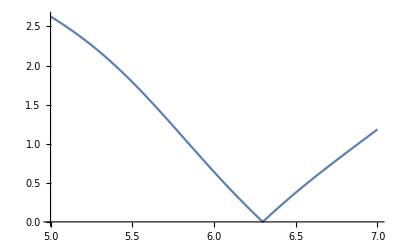

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=7.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521};
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax}
];
Plot[Norm[ySol[t]-yPer],{t,5,7}]
```

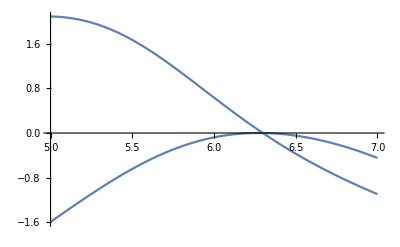

```mathematica
Plot[ySol[t]-yPer,{t,5,7}]
```

```mathematica
tSub=FindRoot[ySol[t][[2]]==yPer[[2]], {t, 6.2}]
ySol[t]/.tSub
yPer
```

Part::partw: Part 2 of InterpolatingFunction[{{0.,7.2}},{5,3,1,{125},{4},0,0,0,0,Automatic,«3»},{{0.,0.0000766691,0.000153338,«6»,0.051148,«115»}},{{{1.99887,-0.0466208},{-0.0466208,-1.97094}},{{1.99886,-0.0467719},{-0.0467719,-1.97084}},«7»,{{1.99393,-0.145807},{-0.145807,-1.90715}},«115»},{Automatic}][t] does not exist.

{t→6.29869}

{1.99958,-0.0466208}

{1.99887,-0.0466208}

Another way to do this is using the EventLocator

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=7.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521};
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==yPer⟦2⟧,Direction->-1,"EventAction":> Print[t]}]
```

Part::partw: Part 2 of y[t] does not exist.

6.29869

InterpolatingFunction[…]

Are there any other periodic orbits?  We are going to talk about this in class.

## Periodic orbits for the Rosseller System

As we saw before there seem to be a lot of near misses for periodic orbits.  Are there periodic orbits?

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=540;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0
},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y'[t]⟦3⟧==0,"Direction"->-1,
"EventAction":> Sow[y[t]]}];
];
m=Length[Data];
TabView[{
"y"->ListPlot[Data⟦All,2⟧,AxesLabel->{"t","y"}],
"z"->ListPlot[Data⟦All,3⟧,AxesLabel->{"t","z"}],
"y vs z"->Graphics[Table[
{Hue[0.9*i/m],PointSize[0.005],Point[Data⟦i,2;;3⟧]},{i, m}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m],
"(y,z)→(y,z)"->Graphics[Table[
{Hue[0.9*i/m],Thickness[0.001],Arrow[{Data⟦i,2;;3⟧,Data⟦i+1,2;;3⟧}]},{i, m-1}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m]
},4]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

1234

Looks like it is stuck in an “almost” loop! How do we get more data?